```mathematica
<<Combinatorica`
<<GraphUtilities`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

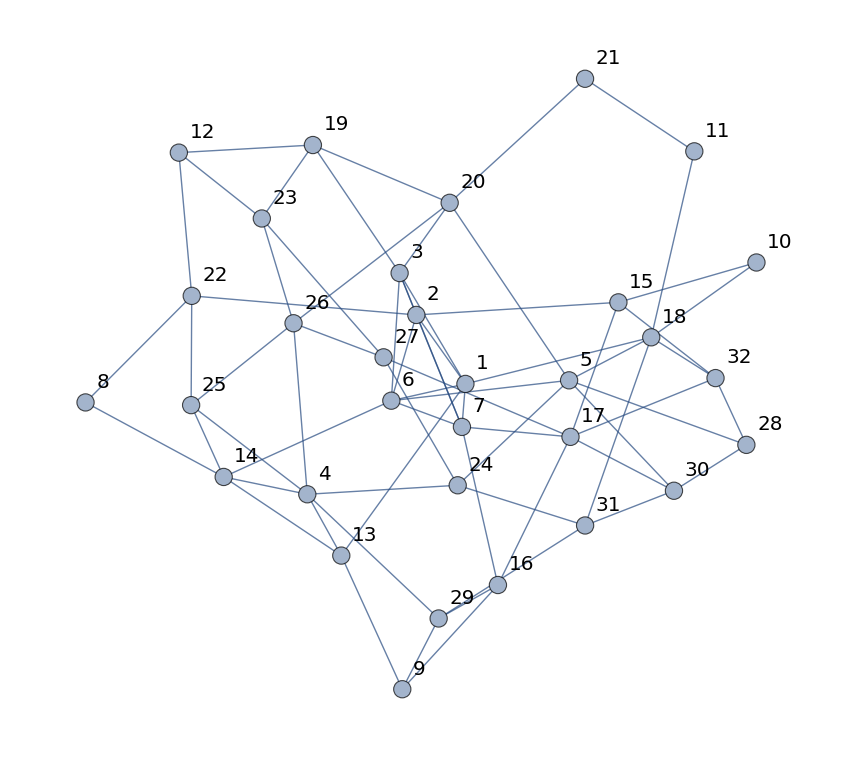

{1,2,3,2,2,4,5,1,3,1,2,3,2,1,2,1,2,2,4,3,2,1,3,1,2,1,1,1,3,3,3,1}

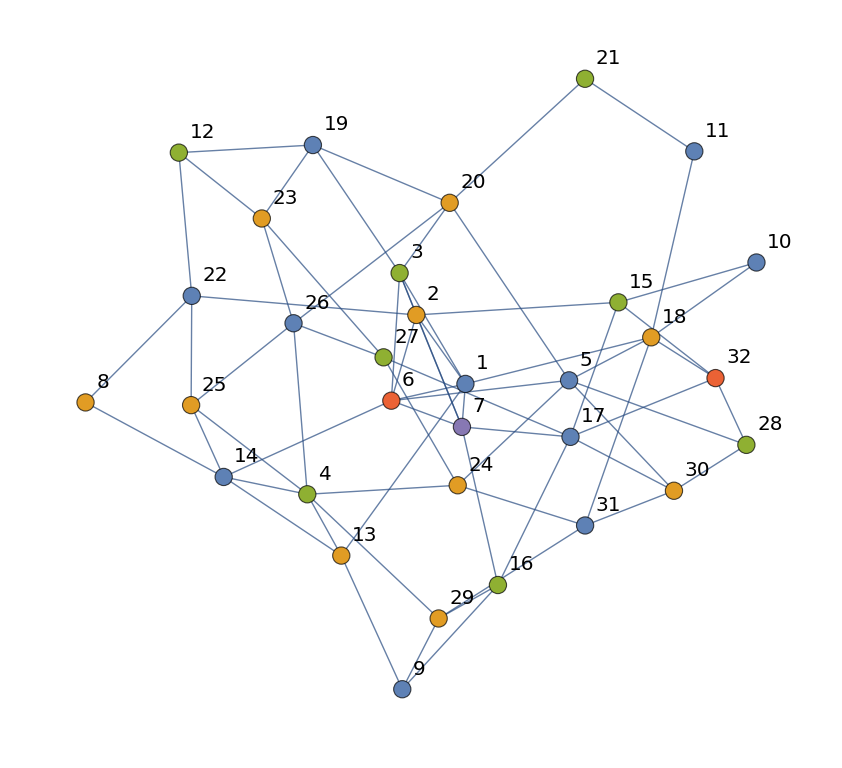

5

{1,2,3,13,18,6,7,22,15,19,20,4,24,14,29,5,30,25,32,28,23,26,16,17,8,9,10,11,21,12,27,31}

{1,2,3,4,18,6,7,22,15,19,20,24,14,29,5,30,25,32,28,23,26,16,17,8,9,10,11,21,13,12}

```mathematica
g=System`Graph[{1<->2,1<->3,1<->13,1<->18,1<->6,1<->7,2<->3,2<->22,2<->15,2<->6,2<->7,3<->19,3<->20,3<->6,3<->7,4<->24,4<->14,4<->29,5<->6,5<->30,6<->7,13<->4,18<->5,22<->25,25<->4,15<->32,32<->28,28<->5,19<->23,23<->26,26<->4,20<->5,24<->5,14<->6,29<->16,16<->7,30<->17,17<->7,8<->14,9<->16,10<->18,11<->21,14<->13,13<->9,16<->17,17<->15,15<->10,18<->11,21<->20,20<->19,19<->12,12<->22,22<->8,12<->23,23<->27,27<->24,24<->31,27<->17,14<->25,25<->26,26<->27,26<->20,9<->29,29<->31,31<->30,30<->28,31<->18,17<->32,32<->18},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]

GColoredList=MinimumVertexColoring@ToCombinatoricaGraph[g]
GColored=SetProperty[g,System`VertexStyle->Thread[System`VertexList[g]->(ColorData[97]/@GColoredList)]]
Max[GColoredList]
VertexList[GColored]
```